# Ejercicio : Maquina de Turing

Estudiante : Andrey Arguedas Espinoza - 2020426569

## Código

## Ejercicio 1

-Graphics-

Definimos las reglas

```mathematica
rules={
{0,"0"}-> {2,"X",1},
{0,"1"}-> {1,"Y",1},
{0,"B"}-> {4,"B",-1},
{0,"Y"}-> {0,"Y",1},
{1,"0"}-> {3,"X",1},
{1,"1"}-> {1,"1",1},
{1,"Y"}-> {1,"Y",1},
{2,"0"}-> {2,"0",1},
{2,"1"}-> {3,"Y",-1},
{2,"Y"}-> {2,"Y",1},
{3,"0"}-> {3,"0",-1},
{3,"1"}-> {3,"0",-1},
{3,"X"}-> {0,"X",1},
{3,"Y"}-> {3,"Y",-1}
};
```

```mathematica
evolution=TuringMachine[rules,{0,{{"0","0","1","1","B"},0}},15]
```

{{{0,1,0},{0,0,1,1,B}},{{2,2,1},{X,0,1,1,B}},{{2,3,2},{X,0,1,1,B}},{{3,2,1},{X,0,Y,1,B}},{{3,1,0},{X,0,Y,1,B}},{{0,2,1},{X,0,Y,1,B}},{{2,3,2},{X,X,Y,1,B}},{{2,4,3},{X,X,Y,1,B}},{{3,3,2},{X,X,Y,Y,B}},{{3,2,1},{X,X,Y,Y,B}},{{0,3,2},{X,X,Y,Y,B}},{{0,4,3},{X,X,Y,Y,B}},{{0,5,4},{X,X,Y,Y,B}},{{4,4,3},{X,X,Y,Y,B}},{{4,4,3},{X,X,Y,Y,B}},{{4,4,3},{X,X,Y,Y,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

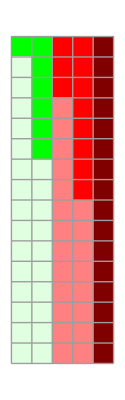

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"0"->Green,"1"->Red, "X" -> LightGreen, "Y" -> Pink},Mesh->True]
```

```mathematica
evolution=TuringMachine[rules,{0,{{"0","1","0","0","1","1","B"},0}},18]
```

{{{0,1,0},{0,1,0,0,1,1,B}},{{2,2,1},{X,1,0,0,1,1,B}},{{3,1,0},{X,Y,0,0,1,1,B}},{{0,2,1},{X,Y,0,0,1,1,B}},{{0,3,2},{X,Y,0,0,1,1,B}},{{2,4,3},{X,Y,X,0,1,1,B}},{{2,5,4},{X,Y,X,0,1,1,B}},{{3,4,3},{X,Y,X,0,Y,1,B}},{{3,3,2},{X,Y,X,0,Y,1,B}},{{0,4,3},{X,Y,X,0,Y,1,B}},{{2,5,4},{X,Y,X,X,Y,1,B}},{{2,6,5},{X,Y,X,X,Y,1,B}},{{3,5,4},{X,Y,X,X,Y,Y,B}},{{3,4,3},{X,Y,X,X,Y,Y,B}},{{0,5,4},{X,Y,X,X,Y,Y,B}},{{0,6,5},{X,Y,X,X,Y,Y,B}},{{0,7,6},{X,Y,X,X,Y,Y,B}},{{4,6,5},{X,Y,X,X,Y,Y,B}},{{4,6,5},{X,Y,X,X,Y,Y,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

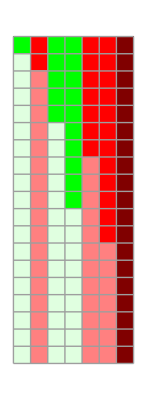

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"0"->Green,"1"->Red, "X" -> LightGreen, "Y" -> Pink},Mesh->True]
```

```mathematica
evolution=TuringMachine[rules,{0,{{"1","0","0","0","1","1","B"},0}},18]
```

{{{0,1,0},{1,0,0,0,1,1,B}},{{1,2,1},{Y,0,0,0,1,1,B}},{{3,3,2},{Y,X,0,0,1,1,B}},{{3,2,1},{Y,X,0,0,1,1,B}},{{0,3,2},{Y,X,0,0,1,1,B}},{{2,4,3},{Y,X,X,0,1,1,B}},{{2,5,4},{Y,X,X,0,1,1,B}},{{3,4,3},{Y,X,X,0,Y,1,B}},{{3,3,2},{Y,X,X,0,Y,1,B}},{{0,4,3},{Y,X,X,0,Y,1,B}},{{2,5,4},{Y,X,X,X,Y,1,B}},{{2,6,5},{Y,X,X,X,Y,1,B}},{{3,5,4},{Y,X,X,X,Y,Y,B}},{{3,4,3},{Y,X,X,X,Y,Y,B}},{{0,5,4},{Y,X,X,X,Y,Y,B}},{{0,6,5},{Y,X,X,X,Y,Y,B}},{{0,7,6},{Y,X,X,X,Y,Y,B}},{{4,6,5},{Y,X,X,X,Y,Y,B}},{{4,6,5},{Y,X,X,X,Y,Y,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

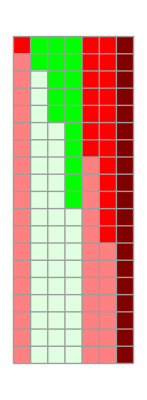

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"0"->Green,"1"->Red, "X" -> LightGreen, "Y" -> Pink},Mesh->True]
```

## Ejercicio 2

-Graphics-

Definimos las reglas

```mathematica
rules={
{0,"a"}-> {1,"X",1},
{1,"a"}-> {1,"a",1},
{1,"b"}-> {2,"Y",1},
{1,"Y"}-> {1,"Y",1},
{2,"b"}-> {2,"b",1},
{2,"Y"}-> {2,"Y",1},
{2,"Z"}-> {2,"Z",1},
{2,"c"}-> {3,"Z",1},
{2,"B"}-> {5,"B",-1},
{3,"c"}-> {4,"Z",-1},
{3,"B"}-> {4,"B",-1},
{4,"Z"}-> {4,"Z",-1},
{4,"b"}-> {4,"b",-1},
{4,"Y"}-> {4,"Y",-1},
{4,"a"}-> {4,"a",-1},
{4,"B"}-> {5,"B",-1},
{4,"X"}-> {0,"X",1},
{5,"Z"}-> {4,"Z",-1}
};
evolution=TuringMachine[rules,{0,{{"a","b","c","B"},1}},5]
```

{{{0,1,0},{a,b,c,B}},{{1,2,1},{X,b,c,B}},{{2,3,2},{X,Y,c,B}},{{3,4,3},{X,Y,Z,B}},{{4,3,2},{X,Y,Z,B}},{{4,2,1},{X,Y,Z,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

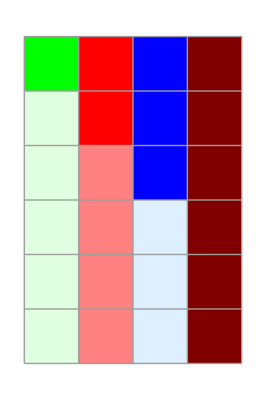

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"a"->Green,"b"->Red,"c"->Blue, "X" -> LightGreen, "Y" -> Pink, "Z" -> LightBlue},Mesh->True]
```

```mathematica
evolution=TuringMachine[rules,{0,{{"a","a","b","b", "c", "c","B"},0}},15]
```

{{{0,1,0},{a,a,b,b,c,c,B}},{{1,2,1},{X,a,b,b,c,c,B}},{{1,3,2},{X,a,b,b,c,c,B}},{{2,4,3},{X,a,Y,b,c,c,B}},{{2,5,4},{X,a,Y,b,c,c,B}},{{3,6,5},{X,a,Y,b,Z,c,B}},{{4,5,4},{X,a,Y,b,Z,Z,B}},{{4,4,3},{X,a,Y,b,Z,Z,B}},{{4,3,2},{X,a,Y,b,Z,Z,B}},{{4,2,1},{X,a,Y,b,Z,Z,B}},{{4,1,0},{X,a,Y,b,Z,Z,B}},{{0,2,1},{X,a,Y,b,Z,Z,B}},{{1,3,2},{X,X,Y,b,Z,Z,B}},{{1,4,3},{X,X,Y,b,Z,Z,B}},{{2,5,4},{X,X,Y,Y,Z,Z,B}},{{2,6,5},{X,X,Y,Y,Z,Z,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

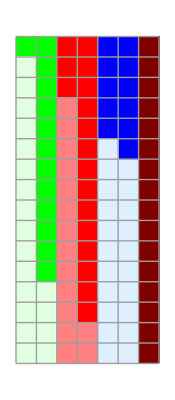

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"a"->Green,"b"->Red,"c"->Blue, "X" -> LightGreen, "Y" -> Pink, "Z" -> LightBlue},Mesh->True]
```

```mathematica
evolution=TuringMachine[rules,{0,{{"a","a","a","b","b","b", "c", "c","c","B"},0}},42]
```

{{{0,1,0},{a,a,a,b,b,b,c,c,c,B}},{{1,2,1},{X,a,a,b,b,b,c,c,c,B}},{{1,3,2},{X,a,a,b,b,b,c,c,c,B}},{{1,4,3},{X,a,a,b,b,b,c,c,c,B}},{{2,5,4},{X,a,a,Y,b,b,c,c,c,B}},{{2,6,5},{X,a,a,Y,b,b,c,c,c,B}},{{2,7,6},{X,a,a,Y,b,b,c,c,c,B}},{{3,8,7},{X,a,a,Y,b,b,Z,c,c,B}},{{4,7,6},{X,a,a,Y,b,b,Z,Z,c,B}},{{4,6,5},{X,a,a,Y,b,b,Z,Z,c,B}},{{4,5,4},{X,a,a,Y,b,b,Z,Z,c,B}},{{4,4,3},{X,a,a,Y,b,b,Z,Z,c,B}},{{4,3,2},{X,a,a,Y,b,b,Z,Z,c,B}},{{4,2,1},{X,a,a,Y,b,b,Z,Z,c,B}},{{4,1,0},{X,a,a,Y,b,b,Z,Z,c,B}},{{0,2,1},{X,a,a,Y,b,b,Z,Z,c,B}},{{1,3,2},{X,X,a,Y,b,b,Z,Z,c,B}},{{1,4,3},{X,X,a,Y,b,b,Z,Z,c,B}},{{1,5,4},{X,X,a,Y,b,b,Z,Z,c,B}},{{2,6,5},{X,X,a,Y,Y,b,Z,Z,c,B}},{{2,7,6},{X,X,a,Y,Y,b,Z,Z,c,B}},{{2,8,7},{X,X,a,Y,Y,b,Z,Z,c,B}},{{2,9,8},{X,X,a,Y,Y,b,Z,Z,c,B}},{{3,10,9},{X,X,a,Y,Y,b,Z,Z,Z,B}},{{4,9,8},{X,X,a,Y,Y,b,Z,Z,Z,B}},{{4,8,7},{X,X,a,Y,Y,b,Z,Z,Z,B}},{{4,7,6},{X,X,a,Y,Y,b,Z,Z,Z,B}},{{4,6,5},{X,X,a,Y,Y,b,Z,Z,Z,B}},{{4,5,4},{X,X,a,Y,Y,b,Z,Z,Z,B}},{{4,4,3},{X,X,a,Y,Y,b,Z,Z,Z,B}},{{4,3,2},{X,X,a,Y,Y,b,Z,Z,Z,B}},{{4,2,1},{X,X,a,Y,Y,b,Z,Z,Z,B}},{{0,3,2},{X,X,a,Y,Y,b,Z,Z,Z,B}},{{1,4,3},{X,X,X,Y,Y,b,Z,Z,Z,B}},{{1,5,4},{X,X,X,Y,Y,b,Z,Z,Z,B}},{{1,6,5},{X,X,X,Y,Y,b,Z,Z,Z,B}},{{2,7,6},{X,X,X,Y,Y,Y,Z,Z,Z,B}},{{2,8,7},{X,X,X,Y,Y,Y,Z,Z,Z,B}},{{2,9,8},{X,X,X,Y,Y,Y,Z,Z,Z,B}},{{2,10,9},{X,X,X,Y,Y,Y,Z,Z,Z,B}},{{5,9,8},{X,X,X,Y,Y,Y,Z,Z,Z,B}},{{4,8,7},{X,X,X,Y,Y,Y,Z,Z,Z,B}},{{4,7,6},{X,X,X,Y,Y,Y,Z,Z,Z,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

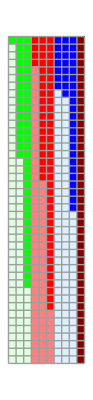

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"a"->Green,"b"->Red,"c"->Blue, "X" -> LightGreen, "Y" -> Pink, "Z" -> LightBlue},Mesh->True]
```

```mathematica
evolution=TuringMachine[rules,{0,{{"a","a","a","a","b","b","b","b", "c", "c","c","c","B"},0}},90]
```

{{{0,1,0},{a,a,a,a,b,b,b,b,c,c,c,c,B}},{{1,2,1},{X,a,a,a,b,b,b,b,c,c,c,c,B}},{{1,3,2},{X,a,a,a,b,b,b,b,c,c,c,c,B}},{{1,4,3},{X,a,a,a,b,b,b,b,c,c,c,c,B}},{{1,5,4},{X,a,a,a,b,b,b,b,c,c,c,c,B}},{{2,6,5},{X,a,a,a,Y,b,b,b,c,c,c,c,B}},{{2,7,6},{X,a,a,a,Y,b,b,b,c,c,c,c,B}},{{2,8,7},{X,a,a,a,Y,b,b,b,c,c,c,c,B}},{{2,9,8},{X,a,a,a,Y,b,b,b,c,c,c,c,B}},{{3,10,9},{X,a,a,a,Y,b,b,b,Z,c,c,c,B}},{{4,9,8},{X,a,a,a,Y,b,b,b,Z,Z,c,c,B}},{{4,8,7},{X,a,a,a,Y,b,b,b,Z,Z,c,c,B}},{{4,7,6},{X,a,a,a,Y,b,b,b,Z,Z,c,c,B}},{{4,6,5},{X,a,a,a,Y,b,b,b,Z,Z,c,c,B}},{{4,5,4},{X,a,a,a,Y,b,b,b,Z,Z,c,c,B}},{{4,4,3},{X,a,a,a,Y,b,b,b,Z,Z,c,c,B}},{{4,3,2},{X,a,a,a,Y,b,b,b,Z,Z,c,c,B}},{{4,2,1},{X,a,a,a,Y,b,b,b,Z,Z,c,c,B}},{{4,1,0},{X,a,a,a,Y,b,b,b,Z,Z,c,c,B}},{{0,2,1},{X,a,a,a,Y,b,b,b,Z,Z,c,c,B}},{{1,3,2},{X,X,a,a,Y,b,b,b,Z,Z,c,c,B}},{{1,4,3},{X,X,a,a,Y,b,b,b,Z,Z,c,c,B}},{{1,5,4},{X,X,a,a,Y,b,b,b,Z,Z,c,c,B}},{{1,6,5},{X,X,a,a,Y,b,b,b,Z,Z,c,c,B}},{{2,7,6},{X,X,a,a,Y,Y,b,b,Z,Z,c,c,B}},{{2,8,7},{X,X,a,a,Y,Y,b,b,Z,Z,c,c,B}},{{2,9,8},{X,X,a,a,Y,Y,b,b,Z,Z,c,c,B}},{{2,10,9},{X,X,a,a,Y,Y,b,b,Z,Z,c,c,B}},{{2,11,10},{X,X,a,a,Y,Y,b,b,Z,Z,c,c,B}},{{3,12,11},{X,X,a,a,Y,Y,b,b,Z,Z,Z,c,B}},{{4,11,10},{X,X,a,a,Y,Y,b,b,Z,Z,Z,Z,B}},{{4,10,9},{X,X,a,a,Y,Y,b,b,Z,Z,Z,Z,B}},{{4,9,8},{X,X,a,a,Y,Y,b,b,Z,Z,Z,Z,B}},{{4,8,7},{X,X,a,a,Y,Y,b,b,Z,Z,Z,Z,B}},{{4,7,6},{X,X,a,a,Y,Y,b,b,Z,Z,Z,Z,B}},{{4,6,5},{X,X,a,a,Y,Y,b,b,Z,Z,Z,Z,B}},{{4,5,4},{X,X,a,a,Y,Y,b,b,Z,Z,Z,Z,B}},{{4,4,3},{X,X,a,a,Y,Y,b,b,Z,Z,Z,Z,B}},{{4,3,2},{X,X,a,a,Y,Y,b,b,Z,Z,Z,Z,B}},{{4,2,1},{X,X,a,a,Y,Y,b,b,Z,Z,Z,Z,B}},{{0,3,2},{X,X,a,a,Y,Y,b,b,Z,Z,Z,Z,B}},{{1,4,3},{X,X,X,a,Y,Y,b,b,Z,Z,Z,Z,B}},{{1,5,4},{X,X,X,a,Y,Y,b,b,Z,Z,Z,Z,B}},{{1,6,5},{X,X,X,a,Y,Y,b,b,Z,Z,Z,Z,B}},{{1,7,6},{X,X,X,a,Y,Y,b,b,Z,Z,Z,Z,B}},{{2,8,7},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{2,9,8},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{2,10,9},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{2,11,10},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{2,12,11},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{2,13,12},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{5,12,11},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{4,11,10},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{4,10,9},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{4,9,8},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{4,8,7},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{4,7,6},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{4,6,5},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{4,5,4},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{4,4,3},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{4,3,2},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{0,4,3},{X,X,X,a,Y,Y,Y,b,Z,Z,Z,Z,B}},{{1,5,4},{X,X,X,X,Y,Y,Y,b,Z,Z,Z,Z,B}},{{1,6,5},{X,X,X,X,Y,Y,Y,b,Z,Z,Z,Z,B}},{{1,7,6},{X,X,X,X,Y,Y,Y,b,Z,Z,Z,Z,B}},{{1,8,7},{X,X,X,X,Y,Y,Y,b,Z,Z,Z,Z,B}},{{2,9,8},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{2,10,9},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{2,11,10},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{2,12,11},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{2,13,12},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{5,12,11},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{4,11,10},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{4,10,9},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{4,9,8},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{4,8,7},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{4,7,6},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{4,6,5},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{4,5,4},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{4,4,3},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{0,5,4},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{0,5,4},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{0,5,4},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{0,5,4},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{0,5,4},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{0,5,4},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{0,5,4},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{0,5,4},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{0,5,4},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{0,5,4},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}},{{0,5,4},{X,X,X,X,Y,Y,Y,Y,Z,Z,Z,Z,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

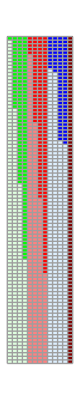

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"a"->Green,"b"->Red,"c"->Blue, "X" -> LightGreen, "Y" -> Pink, "Z" -> LightBlue},Mesh->True]
```

## Nota : Aquí vemos como un ejemplo no valido se queda “stuck” y no logra cambiar la ultima “c”

```mathematica
evolution=TuringMachine[rules,{0,{{"a","a","b","c", "c","c","B"},0}},25]
```

{{{0,1,0},{a,a,b,c,c,c,B}},{{1,2,1},{X,a,b,c,c,c,B}},{{1,3,2},{X,a,b,c,c,c,B}},{{2,4,3},{X,a,Y,c,c,c,B}},{{3,5,4},{X,a,Y,Z,c,c,B}},{{4,4,3},{X,a,Y,Z,Z,c,B}},{{4,3,2},{X,a,Y,Z,Z,c,B}},{{4,2,1},{X,a,Y,Z,Z,c,B}},{{4,1,0},{X,a,Y,Z,Z,c,B}},{{0,2,1},{X,a,Y,Z,Z,c,B}},{{1,3,2},{X,X,Y,Z,Z,c,B}},{{1,4,3},{X,X,Y,Z,Z,c,B}},{{1,4,3},{X,X,Y,Z,Z,c,B}},{{1,4,3},{X,X,Y,Z,Z,c,B}},{{1,4,3},{X,X,Y,Z,Z,c,B}},{{1,4,3},{X,X,Y,Z,Z,c,B}},{{1,4,3},{X,X,Y,Z,Z,c,B}},{{1,4,3},{X,X,Y,Z,Z,c,B}},{{1,4,3},{X,X,Y,Z,Z,c,B}},{{1,4,3},{X,X,Y,Z,Z,c,B}},{{1,4,3},{X,X,Y,Z,Z,c,B}},{{1,4,3},{X,X,Y,Z,Z,c,B}},{{1,4,3},{X,X,Y,Z,Z,c,B}},{{1,4,3},{X,X,Y,Z,Z,c,B}},{{1,4,3},{X,X,Y,Z,Z,c,B}},{{1,4,3},{X,X,Y,Z,Z,c,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

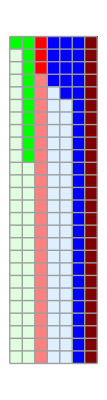

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"a"->Green,"b"->Red,"c"->Blue, "X" -> LightGreen, "Y" -> Pink, "Z" -> LightBlue},Mesh->True]
```

## Ejercicio 3

Definimos las reglas

```mathematica
rules={
{0,"0"}-> {1,"B",1},
{0,"1"}-> {4,"B",1},
{1,"0"}-> {1,"0",1},
{1,"1"}-> {1,"1",1},
{1,"B"}-> {2,"B",-1},
{2,"0"}-> {3,"B",-1},
{3,"0"}-> {3,"0",-1},
{3,"1"}-> {3,"1",-1},
{3,"B"}-> {0,"B",1},
{4,"0"}-> {4,"0",1},
{4,"1"}-> {4,"1",1},
{4,"B"}-> {5,"B",-1},
{5,"1"}-> {6,"B",-1},
{6,"0"}-> {6,"0",-1},
{6,"1"}-> {6,"1",-1},
{6,"B"}-> {0,"B",1}
};
```

Comenzamos a correr las máquinas de Turing y a graficar

```mathematica
evolution=TuringMachine[rules,{0,{{"1","1","B"},0}},4]
```

{{{0,1,0},{1,1,B}},{{4,2,1},{B,1,B}},{{4,3,2},{B,1,B}},{{5,2,1},{B,1,B}},{{6,1,0},{B,B,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

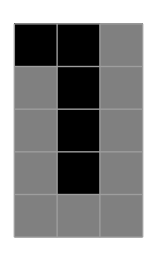

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"1"->Black,"0"->White,"B"->Gray},Mesh->True]
```

```mathematica
evolution=TuringMachine[rules,{0,{{"0","0","B"},0}},4]
```

{{{0,1,0},{0,0,B}},{{1,2,1},{B,0,B}},{{1,3,2},{B,0,B}},{{2,2,1},{B,0,B}},{{3,1,0},{B,B,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

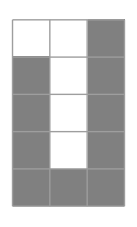

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"1"->Black,"0"->White,"B"->Gray},Mesh->True]
```

```mathematica
evolution=TuringMachine[rules,{0,{{"0","0","0","0","B"},0}},15]
```

{{{0,1,0},{0,0,0,0,B}},{{1,2,1},{B,0,0,0,B}},{{1,3,2},{B,0,0,0,B}},{{1,4,3},{B,0,0,0,B}},{{1,5,4},{B,0,0,0,B}},{{2,4,3},{B,0,0,0,B}},{{3,3,2},{B,0,0,B,B}},{{3,2,1},{B,0,0,B,B}},{{3,1,0},{B,0,0,B,B}},{{0,2,1},{B,0,0,B,B}},{{1,3,2},{B,B,0,B,B}},{{1,4,3},{B,B,0,B,B}},{{2,3,2},{B,B,0,B,B}},{{3,2,1},{B,B,B,B,B}},{{0,3,2},{B,B,B,B,B}},{{0,3,2},{B,B,B,B,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

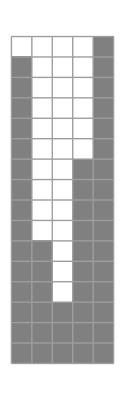

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"1"->Black,"0"->White,"B"->Gray},Mesh->True]
```

```mathematica
evolution=TuringMachine[rules,{0,{{"1","1","1","1","B"},0}},16]
```

{{{0,1,0},{1,1,1,1,B}},{{4,2,1},{B,1,1,1,B}},{{4,3,2},{B,1,1,1,B}},{{4,4,3},{B,1,1,1,B}},{{4,5,4},{B,1,1,1,B}},{{5,4,3},{B,1,1,1,B}},{{6,3,2},{B,1,1,B,B}},{{6,2,1},{B,1,1,B,B}},{{6,1,0},{B,1,1,B,B}},{{0,2,1},{B,1,1,B,B}},{{4,3,2},{B,B,1,B,B}},{{4,4,3},{B,B,1,B,B}},{{5,3,2},{B,B,1,B,B}},{{6,2,1},{B,B,B,B,B}},{{0,3,2},{B,B,B,B,B}},{{0,3,2},{B,B,B,B,B}},{{0,3,2},{B,B,B,B,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

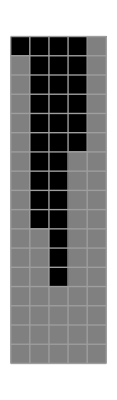

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"1"->Black,"0"->White,"B"->Gray},Mesh->True]
```

```mathematica
evolution=TuringMachine[rules,{0,{{"0","1","0","0","1","0","B"},0}},28]
```

{{{0,1,0},{0,1,0,0,1,0,B}},{{1,2,1},{B,1,0,0,1,0,B}},{{1,3,2},{B,1,0,0,1,0,B}},{{1,4,3},{B,1,0,0,1,0,B}},{{1,5,4},{B,1,0,0,1,0,B}},{{1,6,5},{B,1,0,0,1,0,B}},{{1,7,6},{B,1,0,0,1,0,B}},{{2,6,5},{B,1,0,0,1,0,B}},{{3,5,4},{B,1,0,0,1,B,B}},{{3,4,3},{B,1,0,0,1,B,B}},{{3,3,2},{B,1,0,0,1,B,B}},{{3,2,1},{B,1,0,0,1,B,B}},{{3,1,0},{B,1,0,0,1,B,B}},{{0,2,1},{B,1,0,0,1,B,B}},{{4,3,2},{B,B,0,0,1,B,B}},{{4,4,3},{B,B,0,0,1,B,B}},{{4,5,4},{B,B,0,0,1,B,B}},{{4,6,5},{B,B,0,0,1,B,B}},{{5,5,4},{B,B,0,0,1,B,B}},{{6,4,3},{B,B,0,0,B,B,B}},{{6,3,2},{B,B,0,0,B,B,B}},{{6,2,1},{B,B,0,0,B,B,B}},{{0,3,2},{B,B,0,0,B,B,B}},{{1,4,3},{B,B,B,0,B,B,B}},{{1,5,4},{B,B,B,0,B,B,B}},{{2,4,3},{B,B,B,0,B,B,B}},{{3,3,2},{B,B,B,B,B,B,B}},{{0,4,3},{B,B,B,B,B,B,B}},{{0,4,3},{B,B,B,B,B,B,B}}}

```mathematica
ListAnimate[Last/@evolution]
```

```mathematica
ArrayPlot[Last /@evolution,ColorRules->{"1"->Black,"0"->White,"B"->Gray},Mesh->True]
```

-Graphics-

### Nota : Si corremos la máquina de Turing con un ejemplo que no es palindrome vemos como se queda “stuck” y no logra cambiar los caracteres a Blank.

```mathematica
evolution=TuringMachine[rules,{0,{{"0","1","1","1","B"},0}},20]
```

{{{0,1,0},{0,1,1,1,B}},{{1,2,1},{B,1,1,1,B}},{{1,3,2},{B,1,1,1,B}},{{1,4,3},{B,1,1,1,B}},{{1,5,4},{B,1,1,1,B}},{{2,4,3},{B,1,1,1,B}},{{2,4,3},{B,1,1,1,B}},{{2,4,3},{B,1,1,1,B}},{{2,4,3},{B,1,1,1,B}},{{2,4,3},{B,1,1,1,B}},{{2,4,3},{B,1,1,1,B}},{{2,4,3},{B,1,1,1,B}},{{2,4,3},{B,1,1,1,B}},{{2,4,3},{B,1,1,1,B}},{{2,4,3},{B,1,1,1,B}},{{2,4,3},{B,1,1,1,B}},{{2,4,3},{B,1,1,1,B}},{{2,4,3},{B,1,1,1,B}},{{2,4,3},{B,1,1,1,B}},{{2,4,3},{B,1,1,1,B}},{{2,4,3},{B,1,1,1,B}}}